# Homework 6

```mathematica
{{Timing, AbsoluteTiming, DownValues, {$RecursionLimit}}}
```

## John Knowles

### 1. Problem 11.1

```mathematica
Clear[e]
e[1]:=1+1
e[n_]:=e[n]=e[n-1]+1/n!
e[10]
e[300]
{$RecursionLimit=6000}
Timing[e[5000]][[1]]
Clear[e]
e[n_]:=1+Plus@@(1/Range[n]!)
Timing[e[5000]][[1]]
```

9864101/3628800

831950573921332826504889539989696731114164990621435334706129616147218488010421630927646853278171864420576199937648119177987591600524631592304101543764210111531345567783654022628761294831981700745728615055453495762152980783314981376515037608136216037426617556089523668406872814067512432926197883190966296920503383166515770955370108294269747972605330690587093698982389475212555253967918939020833444797913081575325019173384780689859480363035919219604731236138445792503905232859609150182769062032158629400202371886078126501637805983628599260376069478915593870004217415589702231797226322947167475008252173154330267716001/306057512216440636035370461297268629388588804173576999416776741259476533176716867465515291422477573349939147888701726368864263907759003154226842927906974559841225476930271954604008012215776252176854255965356903506788725264321896264299365204576448830388909753943489625436053225980776521270822437639449120128678675368305712293681943649956460498166450227716500185176546469340112226034729724066333258583506870150169794168850353752137554910289126407157154830282284937952636580145235233156936482233436799254594095276820608062232812387383880817049600000000000000000000000000000000000000000000000000000000000000000000000000

{6000}

2.8125

0.234375

### 2. Exercise 11.1

```mathematica
Clear[a]
a[1]:=7
a[n_]:=a[n-1]+GCD[n,a[n-1]]
A[n_]:=a[n]=a[n]-a[n-1]
A[9]
```

1

### 3. Problem 11.2

```mathematica
Clear[s,t]
s[1]:=3; s[2]:=5; t[1]:=1;
s[n_]:=s[n]=t[n-1]-t[n-2]+4
t[n_]:=t[n]=t[n-1]+s[n-1]
t[4]==t[3]+s[3]
t[100]
```

True

10000

### 4. Problem 11.3

```mathematica
f[n_]:=n-3/;n≥1000
f[n_]:=f[f[n+6]]/;n<1000
f[1]
f[1003]
```

997

1000

### 5. Problem 11.4

```mathematica
Clear[f]
f[1]:=1;f[4]:=4;
f[n_]:=f[n]=f[Plus@@(IntegerDigits[n]^2)]
Select[Range[100],f[#]==1&]
```

{1,7,10,13,19,23,28,31,32,44,49,68,70,79,82,86,91,94,97,100}

### 6. Exercise 11.2

```mathematica
Clear[f]
f[k_?OddQ]:=x+Plus@@(Power[x,Range[3,k,2]]/Range[3,k,2]!)
f[6]
f[11]
Clear[f]
f[1]:=x
f[k_?OddQ]:=f[k]=f[k-2]+x^k/k!
f[11]
```

f[6]

x+x^3/6+x^5/120+x^7/5040+x^9/362880+x^11/39916800

x+x^3/6+x^5/120+x^7/5040+x^9/362880+x^11/39916800

### 7. Problem 11.5

```mathematica
p[1,x_,y_]:=1
p[n_,x_,y_]:=p[n,x,y]=(x+y-1)(y+1)p[n-1,x,y+2]+(y-y^2)p[n-1,x,y]
p[2,x,y]
Simplify[%]
Simplify[p[3,x,y]==p[3,y,x]]
```

y-y^2+(1+y) (-1+x+y)

-1+x+y+x y

True

## Memoization:

```mathematica
Clear[f]
f[0]:=1; f[1]:=1;
f[n_]:=f[n-1]+f[n-2];
Counts[Flatten[Trace[f[15],f[_]]]]
```

<|f[15]→1,f[14]→1,f[13]→2,f[12]→3,f[11]→5,f[10]→8,f[9]→13,f[8]→21,f[7]→34,f[6]→55,f[5]→89,f[4]→144,f[3]→233,f[2]→377,f[1]→610,f[0]→377|>

```mathematica
AbsoluteTiming[f[35]]
```

{18.9785,14930352}

```mathematica
DownValues[f]
```

{HoldPattern[f[0]]:>1,HoldPattern[f[1]]:>1,HoldPattern[f[n_]]:>f[n-1]+f[n-2]}

```mathematica
Clear[f]
f[0]:=1; f[1]:=1;
f[n_]:=f[n]=f[n-1]+f[n-2]
f[5]
DownValues[f]
AbsoluteTiming[f[35]]
```

8

{HoldPattern[f[0]]:>1,HoldPattern[f[1]]:>1,HoldPattern[f[2]]:>2,HoldPattern[f[3]]:>3,HoldPattern[f[4]]:>5,HoldPattern[f[5]]:>8,HoldPattern[f[n_]]:>(f[n]=f[n-1]+f[n-2])}

{0.000265168,14930352}

### 8. Exercise 1

```mathematica
Clear[p]
p[0]:=0; p[1]:=1;
p[n_]:=(p[n]=2*p[n-1]+p[n-2])/;n≥2
p[100]
Count[Simplify[(p[#]==((1+Sqrt[2])^#-(1-Sqrt[2])^#)/(2 Sqrt[2])&)/@Range[0,100]],True]
```

66992092050551637663438906713182313772

101

### 9. Exercise 2

```mathematica
Clear[Fib]
Fib[k_,n_?Negative]:=0/;n≤0;
Fib[k_,1]:=1;
Fib[k_,n_]:=Fib[k,n]=Sum[Fib[k,n-i],{i,1,k}]
Fib[7,80]
```

225369752979121873161024

### 10. Exercise 3

```mathematica
Clear[Hermite]
Hermite[0]:=1; Hermite[1]:=x;
Hermite[n_]:=(Hermite[n]=x*Hermite[n-1]-D[Hermite[n-1],x])/;n≥2
AbsoluteTiming[Expand[Hermite[20]]]
```

{11.0461,654729075-6547290750 x^2+9820936125 x^4-5237832600 x^6+1309458150 x^8-174594420 x^10+13226850 x^12-581400 x^14+14535 x^16-190 x^18+x^20}

```mathematica
Simplify[SeriesCoefficient[E^(x t-t^(2)/2),{t,0,20}]]==Simplify[Hermite[20]/20!]
```

True

### 11. Exercise 4

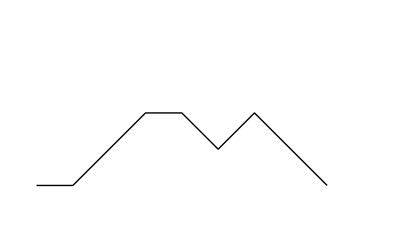

```mathematica
L={{0,0},{1,0},{2,1},{3,2},{4,2},{5,1},{6,2},{7,1},{8,0}};
DrawPath[n_List]:=Graphics[Line[n],PlotRange->{{0,Length[n]},{-1,Length[n]/2}}]
DrawPath[L]
```

```mathematica
Clear[MotzkinPaths]
MotzkinPaths[0]:={{{0,0}}};
MotzkinPaths[1]:={{0,0},{1,0}};
MotzkinPaths[n_]:=Append[MotzkinPaths[n-1],{n,0}]
MotzkinPaths[5]
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0}}

```mathematica
Clear[MotzkinPaths]
MotzkinPaths[0]:={{{0,0}}};
MotzkinPaths[1]:={{0,0},{1,0}};
MatrixForm@Outer[List,Table[Range[1,2],2],{-1,0,1}]
steps[n_]:=Outer[List,Table[Range[1,n],n],{-1,0,1}]
steps[2]
```

((1 | -1
1 | 0
1 | 1) | (2 | -1
2 | 0
2 | 1)
(1 | -1
1 | 0
1 | 1) | (2 | -1
2 | 0
2 | 1))

{{{{1,-1},{1,0},{1,1}},{{2,-1},{2,0},{2,1}}},{{{1,-1},{1,0},{1,1}},{{2,-1},{2,0},{2,1}}}}

```mathematica
L={{0,0},{1,0},{2,1},{3,2},{4,2},{5,1},{6,2},{7,1},{8,0}};
MotzkinPaths[0]:={{{0,0}}};
MotzkinPaths[1]:={{0,0},{1,0}};
DrawPath[L_List]:=Graphics[Line[L]]
MotzkinPaths[n_Integer?Positive]:= AppendTo[MotzkinPaths[0]]
Append[#,{n,0}]&/@MotzkinPaths[n-1](*Accounts for all paths that end in a flat.*)
Join[Append[#,{n,0}]&/@MotzkinPaths[n-1],(*other cases of i go here*)]
(*Join flat ending with down ending.*)
Outer[Append[Function[{a,b},Join[a,#+{i+1,1}&/@b],{n,0}]],MotzkinPaths[i],MotzkinPaths[n-i-2]]
```

MotzkinPaths[{-1+2 n,-1+n}]

Join[MotzkinPaths[{-1+2 n,-1+n}],Null]

Attributes::attnf: n is not a known attribute.

Attributes::attnf: 0 is not a known attribute.

Append::argx: Append[Function[{a,b},Join[a,(#1+{Plus[«2»],1}&)/@b],{n,0}]] called with 2 arguments; 1 argument is expected.

MotzkinPaths[MotzkinPaths[Append[Function[{a,b},Join[a,(#1+{i+1,1}&)/@b],{n,0}]][i,-2-i+n]]]

21

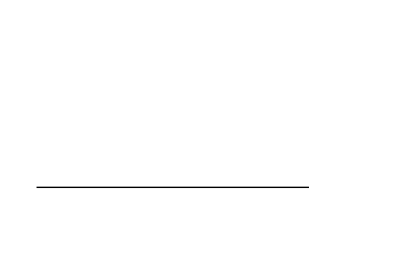
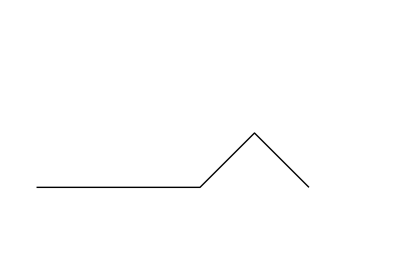
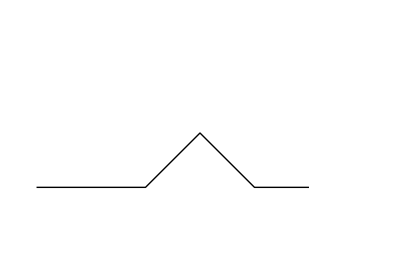
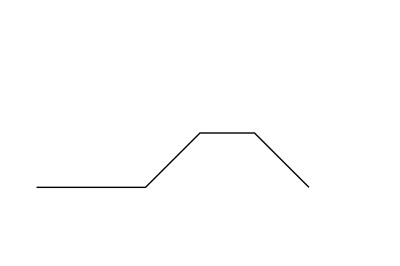
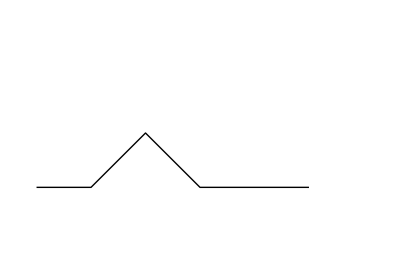
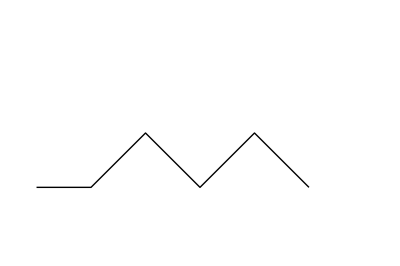
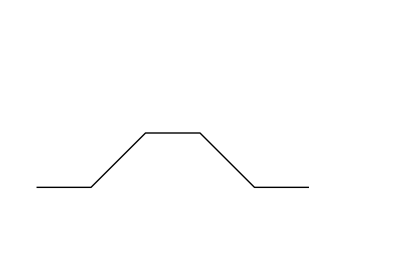
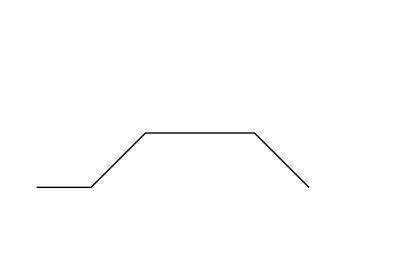

```mathematica
Clear[MotzkinSteps,MotzkinPaths];
MotzkinPaths[0]:={{{0,0}}}; MotzkinPaths[1]:={{{0,0},{1,0}}};
appendSteps[L_List]:={Append[L,-1],Append[L,0],Append[L,1]}
nestSteps[n_Integer]:=Nest[Flatten[Map[appendSteps,#],1]&,{{0}},n]
foldSteps[L_List]:=Rest[FoldList[Plus,0,L]]
MotzkinSteps[n_Integer]:=MotzkinSteps[n]=Select[Map[foldSteps,nestSteps[n]],(Last[#]==0&&FreeQ[#,-1])&]
MotzkinPaths[n_Integer]:=Partition[Partition[Flatten@Inner[List,Range[0,n],Transpose@MotzkinSteps[n],List],2],n+1]
Length[MotzkinPaths[5]]
Map[DrawPath,MotzkinPaths[5]]
```

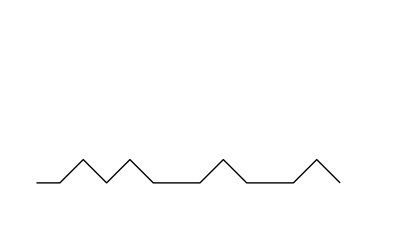

```mathematica
DrawPath[RandomChoice[MotzkinPaths[13]]]
```

```mathematica
AbsoluteTiming[Length[MotzkinPaths[14]]]
```

{24.444,113634}

### 12.

```mathematica
quickSort[L_List]:=Module[{pivot},
If[Length@L≤1,Return[L]];
pivot=RandomChoice@L;
Flatten@{quickSort[Cases[L,a_/;a<pivot]],Cases[L,a_/;a==pivot], quickSort[Cases[L,a_/;a>pivot]]}
]
quickSort[Table[RandomInteger[10000],100]]
```

{111,370,399,495,504,535,552,649,674,743,843,1030,1207,1455,1482,1484,1693,1751,1791,1894,2042,2188,2202,2206,2216,2250,2251,2264,2300,2706,2722,3096,3290,3364,3554,3591,3688,4310,4497,4603,4630,4651,4692,4716,4779,4825,4881,5017,5080,5225,5354,5478,5520,5569,5835,5840,5878,6023,6158,6175,6303,6338,6338,6403,6530,6545,6692,6774,6817,7060,7081,7155,7260,7317,7519,7764,7765,7773,7782,7867,8201,8266,8296,8307,8542,8633,8779,8856,8873,8999,9110,9260,9315,9468,9572,9609,9640,9708,9849,9901}

### 13.

```mathematica
ClearAll["Global`*"]
p={2,8,7,12,6,1,11,4,5,3,9,10};
L={{}};

rowInsert[{{}},x_Integer]:={{x}}
rowInsert[L_List?Length[#]==1&,x_Integer?Positive]:=
If[x>#&/@L,Fold[List,x,L]]

rowInsert[L_List,x_Integer]:=
Do[
If[x<#&/@L[[i]],
rowInsert[L,L[[i,j]]];
ReplacePart[L,{i,j}->x],
If[(i+1)>Length[L],L=Fold[List,x,L],AppendTo[L[[i+1]],x]]
],
{i,1,Length[L]},{j,1,Length [L[[i]]]}
];

n=1;
Schensted[P_List]:=While[n<Length[P],
Print[AppendTo[L,rowInsert[L,P[[n]]]]];n++]

Schensted[p]
```

{{},{{2}}}

{{},{{2}},Null}

{{},{{2}},Null,Null}

{{},{{2}},Null,Null,Null}

{{},{{2}},Null,Null,Null,Null}

{{},{{2}},Null,Null,Null,Null,Null}

{{},{{2}},Null,Null,Null,Null,Null,Null}

{{},{{2}},Null,Null,Null,Null,Null,Null,Null}

{{},{{2}},Null,Null,Null,Null,Null,Null,Null,Null}

{{},{{2}},Null,Null,Null,Null,Null,Null,Null,Null,Null}

{{},{{2}},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

### 14.

```mathematica
Needs["Combinatorica`"]
```

```mathematica
p={2,1,3,6,5,7,10,8,9,4}
Part[p,4]
t=PermutationToTableaux[p]
t[[2]]//TableForm
```

{2,1,3,6,5,7,10,8,9,4}

6

{{{1,3,4,7,8,9},{2,5,10},{6}},{{1,3,4,6,7,9},{2,5,8},{10}}}

1 | 3 | 4 | 6 | 7 | 9
2 | 5 | 8 |  |  | 
10 |  |  |  |  |

```mathematica
ClearAll["Global`*"]
p={2,8,7,12,6,1,11,4,5,3,9,10};
rowInsert[L_List,x_Integer]:=First[rowInsert[L,x,All]]
rowInsert[L_List,x_Integer,All]:={{x},1}
rowInsert[L_List,x_Integer,All]:=Module[{element=x, row=0,col,l=L},
While[row<Length[l], row++; 
If[Last[l[[row]]]≤element,AppendTo[l[[row]],element];
Return[{l,row}]];
col=Position[l[[row]],element/;element!={}];
{element,l[[row,col]]}={l[[row,col]],element};
];
{Append[l,{element}],row+1}
]

Schensted[p_List]:=
Module[{pS={{p[[1]]}},qS={{1}}, r=1},
Do[{pS, r}=rowInsert[pS,p[[x]],All];
If[r≤ Length[qS],AppendTo[qS[[r]],x],AppendTo[qS,{x}]],
{x, 2, Length[p]}];
{pS,qS}
]
Schensted[p]//TableForm
```

2
8
12 |  |  |  |  |  |  |  |  | 
1
2
4 | 3 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12

```mathematica
Clear["Global`*"]
rowInsert[{{}},x_Integer]:={{x}}
rowInsert[{{}},2]
```

{{2}}

### 15.